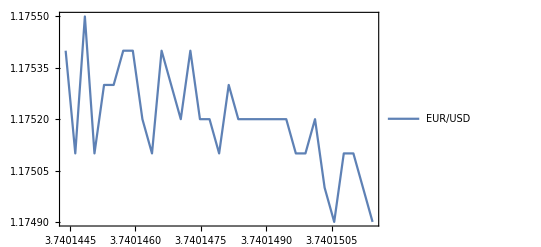

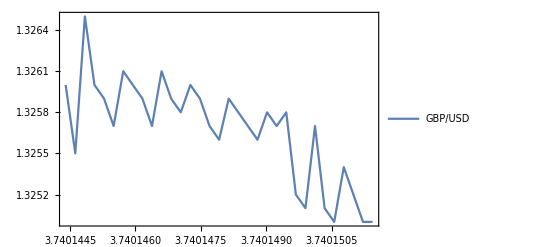

```mathematica
EURUSD=Import["/Users/wanghaibiao/Desktop/hf dk model.xlsx",{"Data",1,Table[i,{i,2,34}],{1,3}}];
eurusd=Import["/Users/wanghaibiao/Desktop/hf dk model.xlsx",{"Data",1,Table[i,{i,2,34}],3}];
GBPUSD=Import["/Users/wanghaibiao/Desktop/hf dk model.xlsx",{"Data",1,Table[i,{i,2,34}],{1,2}}];
gbpusd=Import["/Users/wanghaibiao/Desktop/hf dk model.xlsx",{"Data",1,Table[i,{i,2,34}],2}];
date=Import["/Users/wanghaibiao/Desktop/hf dk model.xlsx",{"Data",1,Table[i,{i,2,34}],1}];
DateListPlot[EURUSD,PlotLegends->Placed[{"EUR/USD"},Above]]
DateListPlot[GBPUSD,PlotLegends->Placed[{"GBP/USD"},Above]]
```

we modify the tick data, there are four ticks in one minute, we just take one tick data. (Ultra tick data can not be fitted by the variance gamma process). Although this extremely small size of data is successful to generate the simulation of exchange rate, however, such small size of the observation, may not successful all the time.

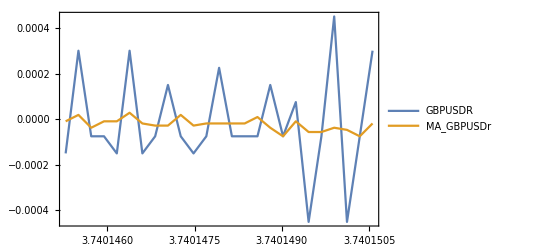

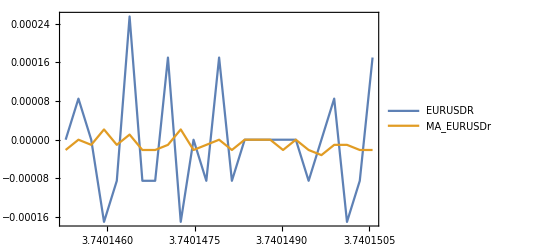

```mathematica
gbpusdr=Differences[Log[gbpusd]];
eurusdr=Differences[Log[eurusd]];
GBPUSDr=Table[{date[[i+4]],gbpusdr[[i+4]]},{i,1,25}];EURUSDr=Table[{date[[i+4]],eurusdr[[i+4]]},{i,1,25}];
mMAgbpusdr=MovingAverage[gbpusdr,8];
mMAeurusdr=MovingAverage[eurusdr,8];
mMAGBPUSDr=Table[{date[[i+4]],mMAgbpusdr[[i]]},{i,1,25}];mMAEURUSDr=Table[{date[[i+4]],mMAeurusdr[[i]]},{i,1,25}];
DateListPlot[{GBPUSDr,mMAGBPUSDr},PlotRange->{All,All},PlotLegends->Placed[{"GBPUSDR","MA_GBPUSDr"},Above]]
DateListPlot[{EURUSDr,mMAEURUSDr},PlotRange->{All,All},PlotLegends->Placed[{"EURUSDR","MA_EURUSDr"},Above]]
```

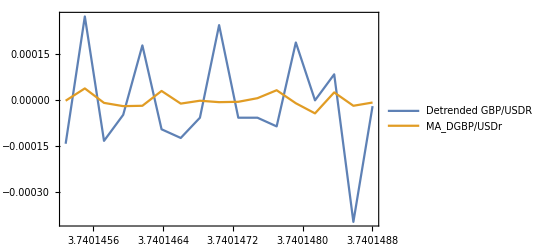

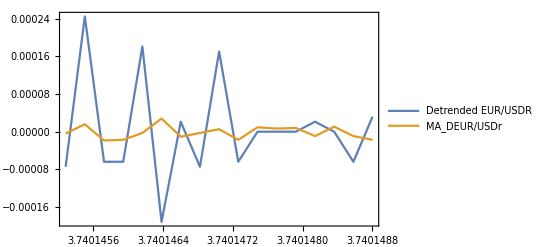

```mathematica
Dgbpusdr= Take[Drop[gbpusdr,4],25]-mMAgbpusdr;
Deurusdr= Take[Drop[eurusdr,4],25]-mMAeurusdr;
DGBPUSDr=Table[{date[[i+4]],Dgbpusdr[[i+4]]},{i,1,17}];
DEURUSDr=Table[{date[[i+4]],Deurusdr[[i+4]]},{i,1,17}];
mMADgbpusdr=MovingAverage[Dgbpusdr,8];
mMADeurusdr=MovingAverage[Deurusdr,8];
mMADGBPUSDr=Table[{date[[i+4]],mMADgbpusdr[[i]]},{i,1,17}];mMADEURUSDr=Table[{date[[i+4]],mMADeurusdr[[i]]},{i,1,17}];
DateListPlot[{DGBPUSDr,mMADGBPUSDr},PlotRange->{All,All},PlotLegends->Placed[{"Detrended GBP/USDR","MA_DGBP/USDr"},Above]]
DateListPlot[{DEURUSDr,mMADEURUSDr},PlotRange->All,PlotLegends->Placed[{"Detrended EUR/USDR","MA_DEUR/USDr"},Above]]
```

```mathematica
NSolve[m+theta==Mean[Dgbpusdr*100]&&sigma^2+theta^2==Variance[Dgbpusdr*100]&&(2*theta^3+3sigma^2*theta)/(sigma^2+theta^2)^1.5==Skewness[Dgbpusdr*100]&&sigma>0,{m,theta,sigma},Reals]
NSolve[m+theta==Mean[Deurusdr*100]&&sigma^2+theta^2==Variance[Deurusdr*100]&&(2*theta^3+3sigma^2*theta)/(sigma^2+theta^2)^1.5==Skewness[Deurusdr*100]&&sigma>0,{m,theta,sigma},Reals]
```

{{theta→0.00174928,sigma→0.0209344,m→-0.000919387}}

{{theta→0.00127757,sigma→0.0112396,m→-0.00102228}}

```mathematica
Subscript[θ, 1]=0.001749276614020261;
Subscript[m, 1]=-0.0009193867469525652;
Subscript[σ, 1]=0.020934433709315484;
Subscript[θ, 2]=0.001277566207101511;
Subscript[m, 2]=-0.001022283257626045;
Subscript[σ, 2]=0.011239646926482941;
```

```mathematica
F=Function[x,((2*Exp[Subscript[θ, 1]*(x-Subscript[m, 1])/Subscript[σ, 1]^2])/(Subscript[σ, 1]*Sqrt[2*Pi]*Gamma[1]))*((x-Subscript[m, 1])^2/(2*Subscript[σ, 1]^2+Subscript[θ, 1]^2))^0.25*BesselK[0.5,Sqrt[(x-Subscript[m, 1])^2*(2*Subscript[σ, 1]^2+Subscript[θ, 1]^2)]/Subscript[σ, 1]^2]][x]
```

33.7184 ⅇ^(3.9915 (0.000919387+x)-67.6722 √((0.000919387+x)^2)) (1+0./(√((0.000919387+x)^2)))

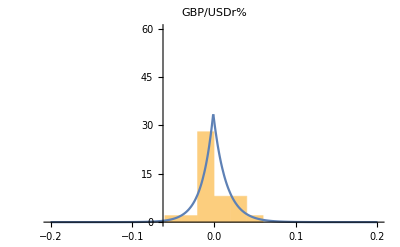

```mathematica
Show[Histogram[Dgbpusdr*100,Automatic,"ProbabilityDensity"],Plot[F,{x,-0.2,0.2},PlotRange->{Full,Full}],PlotRange->{All,{0,60}},PlotLabel->"GBP/USDr%"]
```

```mathematica
G=Function[x,((2*Exp[(Subscript[θ, 2])*(x-Subscript[m, 2])/Subscript[σ, 2]^2])/(Subscript[σ, 2]*Sqrt[2*Pi]*Gamma[1]))*((x-Subscript[m, 2])^2/(2*Subscript[σ, 2]^2+Subscript[θ, 2]^2))^0.25*BesselK[0.5,Sqrt[(x-Subscript[m, 2])^2*(2*Subscript[σ, 2]^2+Subscript[θ, 2]^2)]/Subscript[σ, 2]^2]][x]
```

62.7096 ⅇ^(10.113 (0.00102228+x)-126.229 √((0.00102228+x)^2)) (1+0./(√((0.00102228+x)^2)))

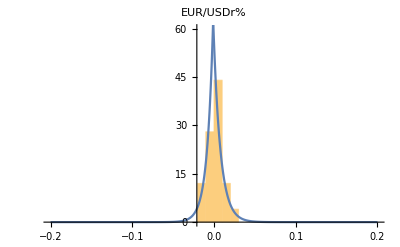

```mathematica
Show[Histogram[Deurusdr*100,Automatic,"ProbabilityDensity"],Plot[G,{x,-0.2,0.2},PlotRange->{Full,Full}],PlotRange->{All,{0,60}},PlotLabel->"EUR/USDr%"]
```

```mathematica
𝒟1=ProbabilityDistribution[F,{x,-Infinity,Infinity}];
DistributionFitTest[Dgbpusdr*100,𝒟1,"PearsonChiSquare"]
𝒟2=ProbabilityDistribution[G,{x,-Infinity,Infinity}];
DistributionFitTest[Deurusdr*100,𝒟2,"PearsonChiSquare"]
```

0.235881

0.070183

```mathematica
R12=Sin[Pi*KendallTau[Dgbpusdr*100,Deurusdr*100]/2];
R={{1,R12},{R12,1}};
MatrixForm[R]
```

(1 | 0.731232
0.731232 | 1)

```mathematica
L1=Dgbpusdr*100;
L2=Deurusdr*100;
```

```mathematica
data=Table[{L1[[i]],L2[[i]]},{i,1,25}];
```

```mathematica
EstimatedDistribution[data,CopulaDistribution[{"MultivariateT",R,v},{StudentTDistribution[v],StudentTDistribution[v]}],ParameterEstimator->"MaximumLikelihood"]
```

CopulaDistribution[{MultivariateT,{{1,0.731232},{0.731232,1}},798.531},{StudentTDistribution[798.531],StudentTDistribution[798.531]}]

```mathematica
ν=1200.4613327688985;
```

```mathematica
A=CholeskyDecomposition[R];
dist=ProductDistribution[NormalDistribution[],NormalDistribution[],ChiSquareDistribution[ν]];
z1=RandomVariate[MarginalDistribution[dist,1],25];
z2=RandomVariate[MarginalDistribution[dist,2],25];
s=RandomVariate[MarginalDistribution[dist,3],25];
For[i=1,i≤25,i++,
Subscript[s, i]=s[[i]];
Subscript[y, i]=A.{z1[[i]],z2[[i]]};
Subscript[x, i]=Sqrt[ν]/Sqrt[Subscript[s, i]]*Subscript[y, i]];
x1=Table[Subscript[x, i][[1]],{i,25}];
x2=Table[Subscript[x, i][[2]],{i,25}];
Subscript[u, 1]=CDF[StudentTDistribution[ν],x1];
Subscript[u, 2]=CDF[StudentTDistribution[ν],x2];
```

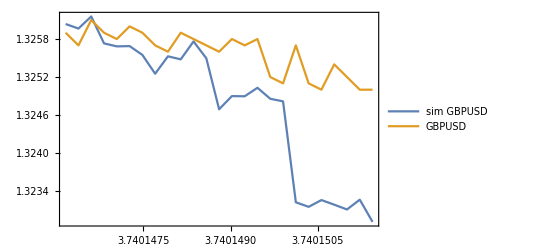

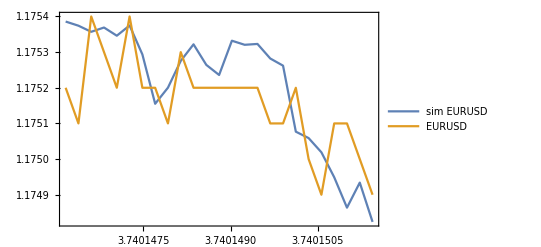

```mathematica
Subscript[Sim1, 0]=Take[Drop[gbpusd,7],1][[1]];
Subscript[Sim2, 0]=Take[Drop[eurusd,7],1][[1]];
S1=Take[Drop[gbpusd,8],25];
S2=Take[Drop[eurusd,8],25];
dates=Take[Drop[date,8],25];
Subscript[L, 1]=InverseCDF[𝒟1,Subscript[u, 1]];
Subscript[L, 2]=InverseCDF[𝒟2,Subscript[u, 2]];
For[t=1,t≤25,t++,
Subscript[L, 1,t]=Subscript[L, 1][[t]];
Subscript[L, 2,t]=Subscript[L, 2][[t]];
Subscript[Sim1, t]=Subscript[Sim1, t-1]*Exp[mMAgbpusdr[[t]]+Subscript[L, 1,t]/100];
Subscript[Sim2, t]=Subscript[Sim2, t-1]*Exp[mMAeurusdr[[t]]+Subscript[L, 2,t]/100]];
Sm1=Table[{dates[[t]],Subscript[Sim1, t]},{t,1,25}];
Sm2=Table[{dates[[t]],Subscript[Sim2, t]},{t,1,25}];
DateListPlot[{Sm1,Table[{dates[[t]],S1[[t]]},{t,1,25}]},PlotLegends->Placed[{"sim tick GBPUSD","GBPUSD"},Above]]
DateListPlot[{Sm2,Table[{dates[[t]],S2[[t]]},{t,1,25}]},PlotLegends->Placed[{"sim tick EURUSD","EURUSD"},Above]]
```